```mathematica
(* Wymiary auta - dlugosc = a, szerokosc = b, promień koła - R. Punkt odniesienia modelu - srodek geometryczny *)
```

```mathematica
(* Współrzędne uogólnione samochodu: polożenie (x,y), orientacja - ϕ, kąt skrętu kół - δ, kąt obrotu tylnich kół (napęd na tył) - θ *)
```

```mathematica
q[t_] := Transpose[{{x[t],y[t],ϕ[t],δ[t],θ[t]}}]
```

```mathematica
(* Wyprowadzenie ograniczeń na poślizgi boczne *)
```

```mathematica
(* współrzędne środka osi tylnich kół *)
xt[t_] := x[t] - a*Cos[ϕ[t]]/2; 
yt[t_] := y[t] - a*Sin[ϕ[t]]/2;
(* współrzędne środka osi przednich kół *)
xp[t_] := x[t] + a*Cos[ϕ[t]]/2;
yp[t_] := y[t] + a*Sin[ϕ[t]]/2;
```

```mathematica
(* Warunek na brak poślizgu kół tylnich *)
FullSimplify[D[xt[t],t]*Sin[ϕ[t]] - D[yt[t],t]*Cos[ϕ[t]]] ==0
```

Sin[ϕ[t]] x'[t]-Cos[ϕ[t]] y'[t]+1/2 a ϕ'[t]==0

```mathematica
(* Warunek na brak poślizgu kół przednich *)
FullSimplify[D[xp[t],t]*Sin[ϕ[t]+δ[t]] - D[yp[t],t]*Cos[ϕ[t]+δ[t]]] ==0
```

Sin[δ[t]+ϕ[t]] x'[t]-Cos[δ[t]+ϕ[t]] y'[t]-1/2 a Cos[δ[t]] ϕ'[t]==0

```mathematica
(* Warunek na brak poślizgu wzdłużnego kół tylnich *)
FullSimplify[D[xt[t],t]*Cos[ϕ[t]] + D[yt[t],t]*Sin[ϕ[t]]-R*D[θ[t],t]] ==0
```

Cos[ϕ[t]] x'[t]+Sin[ϕ[t]] y'[t]-R θ'[t]==0

```mathematica
(* Postać Pfaffa *)
Pfaff[t_]:={{Sin[ϕ[t]], -Cos[ϕ[t]], a/2, 0, 0},{Sin[δ[t]+ϕ[t]], -Cos[δ[t]+ϕ[t]], -a*Cos[δ[t]]/2, 0, 0},{Cos[ϕ[t]], Sin[ϕ[t]], 0, 0, -R}};
MatrixForm[Pfaff[t]]
```

(Sin[ϕ[t]] | -Cos[ϕ[t]] | a/2 | 0 | 0
Sin[δ[t]+ϕ[t]] | -Cos[δ[t]+ϕ[t]] | -1/2 a Cos[δ[t]] | 0 | 0
Cos[ϕ[t]] | Sin[ϕ[t]] | 0 | 0 | -R)

```mathematica
(* Macierz sterowania *)
GMatrix[t_] := Transpose[FullSimplify[Expand[NullSpace[Pfaff[t]]]]];
MatrixForm[GMatrix[t]]
```

(R Cos[ϕ[t]]-1/2 R Sin[ϕ[t]] Tan[δ[t]] | 0
R Sin[ϕ[t]]+1/2 R Cos[ϕ[t]] Tan[δ[t]] | 0
(R Tan[δ[t]])/a | 0
0 | 1
1 | 0)

```mathematica
(* Równania kinematyki, sterowania oznaczają tutaj prędkości *)
u[t_] := {{u1[t]},{u2[t]}};
MatrixForm[D[q[t],t]] == MatrixForm[GMatrix[t].u[t]]
```

(x'[t]
y'[t]
ϕ'[t]
δ'[t]
θ'[t])==((R Cos[ϕ[t]]-1/2 R Sin[ϕ[t]] Tan[δ[t]]) u1[t]
(R Sin[ϕ[t]]+1/2 R Cos[ϕ[t]] Tan[δ[t]]) u1[t]
(R Tan[δ[t]] u1[t])/a
u2[t]
u1[t])

```mathematica
(* ============================================ Dynamika ==================================== *)
```

```mathematica
(* Macierz bezwładności - zapytam jeszcze Tchonia, czy nie da się jakoś bardziej jej skomplikować *)
(* mc - masa całkowita, Ic - moment bezwładności, Ikier - bezwładność kierownicy, Ikol - bezwładność kół napędowych *)
Q=DiagonalMatrix[{mc,mc,Ic,Ikier,Ikol}];
(* Macierz sterowania, UWAGA - sterowania u to przyspieszenia *)
B = {{0,0},{0,0},{0,0},{0,1},{1,0}};
```

```mathematica
(* Lagrange *)
L[q_,qp_]:=Transpose[qp].Q.qp/2; (* Tylko energia kinetyczna, potencjalna pomijalna, jako że zamierzamy jeździć po płaskim *)
L[q[t],D[q[t],t]]
```

{{1/2 (mc x'[t]^2+mc y'[t]^2+Ikier δ'[t]^2+Ikol θ'[t]^2+Ic ϕ'[t]^2)}}

```mathematica
(* Równania ruchu z zasady d'Alemberta *)
lambdavec = Transpose[{{λ1,λ2,λ3}}];
(* Formalny zapis: *)
MatrixForm[Transpose[D[D[L[q[t],D[q[t],t]],Transpose[D[q[t],t]]],t][[1]]] - Transpose[D[L[q[t],q[t]],Transpose[D[q[t],t]]][[1]]] ] == MatrixForm[Transpose[Pfaff[t]].lambdavec] + MatrixForm[B.u[t]]
```

(mc x''[t]
mc y''[t]
Ic ϕ''[t]
Ikier δ''[t]
Ikol θ''[t])==(0
0
0
u2[t]
u1[t])+(λ3 Cos[ϕ[t]]+λ1 Sin[ϕ[t]]+λ2 Sin[δ[t]+ϕ[t]]
-λ1 Cos[ϕ[t]]-λ2 Cos[δ[t]+ϕ[t]]+λ3 Sin[ϕ[t]]
(a λ1)/2-1/2 a λ2 Cos[δ[t]]
0
-R λ3)

```mathematica
(* Ale w tym przypadku to samo otrzymujemy prostszym wzorem (macierz Q jest stała) *)
```

```mathematica
MatrixForm[Q.D[D[q[t],t],t]] == MatrixForm[Transpose[Pfaff[t]].lambdavec] + MatrixForm[B.u[t]]
```

(mc x''[t]
mc y''[t]
Ic ϕ''[t]
Ikier δ''[t]
Ikol θ''[t])==(0
0
0
u2[t]
u1[t])+(λ3 Cos[ϕ[t]]+λ1 Sin[ϕ[t]]+λ2 Sin[δ[t]+ϕ[t]]
-λ1 Cos[ϕ[t]]-λ2 Cos[δ[t]+ϕ[t]]+λ3 Sin[ϕ[t]]
(a λ1)/2-1/2 a λ2 Cos[δ[t]]
0
-R λ3)

```mathematica
(* Żeby wyeliminować λ, które chujowo się liczy, transformujemy układ poprzez podstawienie D[q[t],t] = G.η[t] - czyli po prostu wrzucamy do równań policzoną kinematykę; W tym wypadku η reprezentują sobą sterowania prędkościowe dla kinematyki *)
η[t_] := {{η1[t]},{η2[t]}};
(* Równania na D[η[t],t] *)
MatrixForm[D[η[t],t]] ==MatrixForm[FullSimplify[Inverse[(Transpose[GMatrix[t]].Q.GMatrix[t])]].(FullSimplify[-Transpose[GMatrix[t]].Q.Simplify[D[GMatrix[t],t]].η[t]] + Transpose[GMatrix[t]].B.u[t])]
```

(η1'[t]
η2'[t])==((8 a^2 Cos[δ[t]]^2 (u1[t]-((4 Ic+a^2 mc) R^2 Sec[δ[t]]^2 Tan[δ[t]] η1[t] δ'[t])/(4 a^2)))/(4 Ic R^2+a^2 (4 Ikol+5 mc R^2)+(-4 Ic R^2+a^2 (4 Ikol+3 mc R^2)) Cos[2 δ[t]])
u2[t]/Ikier)

```mathematica
(* I dla kompletu kinematyka (sterowanie 1 - prędkość kół napędowych, sterowanie 2 - prędkość skrętu kierownicy). Teraz można to wrzucić w Matlaba, puścić symulację i będzie jeździć. Wizualizację mogę zrobić potem, jak potrzeba. *)
MatrixForm[D[q[t],t]] == MatrixForm[GMatrix[t].η[t]]
```

(x'[t]
y'[t]
ϕ'[t]
δ'[t]
θ'[t])==((R Cos[ϕ[t]]-1/2 R Sin[ϕ[t]] Tan[δ[t]]) η1[t]
(R Sin[ϕ[t]]+1/2 R Cos[ϕ[t]] Tan[δ[t]]) η1[t]
(R Tan[δ[t]] η1[t])/a
η2[t]
η1[t])

```mathematica
(* No to rozwiązujemy, deklaracje równań i takie tam pierdoły zwijające to w odpowiednią formę, a potem na solwer. Na wykresie trajektoria przy stałych przyspieszeniach *)
```

```mathematica
Rownania[t_]:=Join[Table[D[η[t],t][[i]][[1]]==(FullSimplify[Inverse[(Transpose[GMatrix[t]].Q.GMatrix[t])]].(FullSimplify[-Transpose[GMatrix[t]].Q.Simplify[D[GMatrix[t],t]].η[t]] + Transpose[GMatrix[t]].B.u[t]))[[i]][[1]],{i,2}]/.{u1[t]->5,u2[t]->0.1},Table[η[0][[i]][[1]]==0,{i,2}],Table[D[q[t],t][[i]][[1]] == (GMatrix[t].η[t])[[i]][[1]],{i,5}],Table[q[0][[i]][[1]]==0,{i,5}]];
```

```mathematica
Stale = {R->0.1,a->1,mc->100,Ic->1,Ikier->10,Ikol->10};
```

```mathematica
MatrixForm[D[Join[η[t],q[t]],t]] == MatrixForm[Join[FullSimplify[Inverse[(Transpose[GMatrix[t]].Q.GMatrix[t])]].(FullSimplify[-Transpose[GMatrix[t]].Q.Simplify[D[GMatrix[t],t]].η[t]] + Transpose[GMatrix[t]].B.u[t]),GMatrix[t].η[t]]]
```

(η1'[t]
η2'[t]
x'[t]
y'[t]
ϕ'[t]
δ'[t]
θ'[t])==((8 a^2 Cos[δ[t]]^2 (u1[t]-((4 Ic+a^2 mc) R^2 Sec[δ[t]]^2 Tan[δ[t]] η1[t] δ'[t])/(4 a^2)))/(4 Ic R^2+a^2 (4 Ikol+5 mc R^2)+(-4 Ic R^2+a^2 (4 Ikol+3 mc R^2)) Cos[2 δ[t]])
u2[t]/Ikier
(R Cos[ϕ[t]]-1/2 R Sin[ϕ[t]] Tan[δ[t]]) η1[t]
(R Sin[ϕ[t]]+1/2 R Cos[ϕ[t]] Tan[δ[t]]) η1[t]
(R Tan[δ[t]] η1[t])/a
η2[t]
η1[t])

```mathematica
rozwiazanie = NDSolve[Rownania[t]/.Stale,Join[Transpose[q[t]][[1]],Transpose[η[t]][[1]]],{t,0,20}];
```

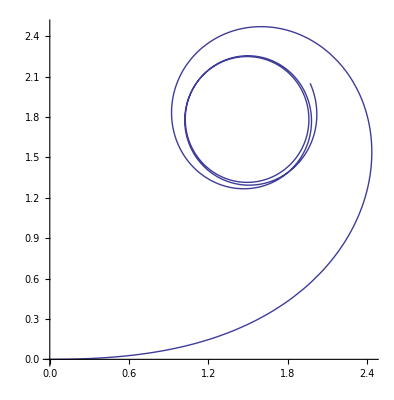

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}]/.rozwiazanie,{t,0,20}]
```